# Stable Sankey Notebook

I've tried to clean out most of the garbage from the mass of code that's been floating around.  Everything needed to produce the diagrams should be contained in the source section.  I included some examples that draw on data I've pushed to github.

## Source

### Book-keeping

```mathematica
(*This is a function which returns the slope from the right top of the ith node to the left bottom of the jth.  We'll use this to set the order in which strands branch off from a node. *)
slope[pair_,strandList_,nodeNameList_]:=(#[[2]])/(#[[1]])&[((rects[strandList,nodeNameList][[#[[2]],1 ]]+rects[strandList,nodeNameList][[#[[2]],2 ]])/2-(rects[strandList,nodeNameList][[#[[1]],1 ]]+rects[strandList,nodeNameList][[#[[1]],2 ]])/2)&[pair]];
(*Function to reflect a point about a given y value.*)
vertReflect[y_]:={#[[1]],2y-#[[2]]}&;

midpoint[node_,nodeNameList_]:=rowNum[node,nodeNameList] betweenSpace[[columnNum[node,nodeNameList]]]+startys[[columnNum[node,nodeNameList]]]+normalizer*(maxBreadth[[columnNum[node,nodeNameList],rowNum[node,nodeNameList]]]/2+Plus@@maxBreadth[[columnNum[node,nodeNameList],;;(rowNum[node,nodeNameList]-1)]]);

(*This determines the order that the strands branch from nodes.  Given two strands originating from same node:  If same column, use y position of end nodes.  If different columns, compare y pos of beginning node with y pos of end node in closest column*)
strandOrderCompare[strand1_,strand2_,nodeNameList_]:=If[strand1[[1]]==strand2[[1]](*share a start*),
If[columnNum[strand1[[2]],nodeNameList]==columnNum[strand2[[2]],nodeNameList](*end in same column*),strand1[[2]]<strand2[[2]],
(*end in diff columns*) If[columnNum[strand1[[2]],nodeNameList]<columnNum[strand2[[2]],nodeNameList],
midpoint[strand1[[2]],nodeNameList]<midpoint[strand1[[1]],nodeNameList],
midpoint[strand2[[2]],nodeNameList]>midpoint[strand1[[1]],nodeNameList]]],

If[strand1[[2]]==strand2[[2]](*Share an end, not a start*),midpoint[strand1[[1]],nodeNameList]<midpoint[strand2[[1]],nodeNameList],

(*Don't share a start or end*)midpoint[strand1[[1]],nodeNameList]<midpoint[strand2[[1]],nodeNameList]
]
];

(*This function will take a node i, and return the column number in which it resides.*)
columnNum[index_,nodeNameList_]:=First[Position[nodeNameList,Flatten[nodeNameList][[index]]]][[1]];
rowNum[index_,nodeNameList_]:=First[Position[nodeNameList,Flatten[nodeNameList][[index]]]][[2]];

(*Convert Quads to other energy units*)
unitConvert[QuadValue_,newUnits_]:=N[10^-3 Round[10^3 N[Piecewise[{{QuadValue,newUnits=="Quads"},{.0334*QuadValue,newUnits=="TW"},{.0334*10^3*QuadValue,newUnits=="GW"},{.0334*10^9*QuadValue,newUnits=="kW"},{5800000000000/10^15*QuadValue,newUnits=="MBarrels Crude Oil"}}],3]]];

(*This computes the CO2 emissions at each node by adding the inputs for each node.  We'll keep the list structure of nodeNames for convenience.*)
co2e[strandMatrix_,nodeNameList_(*This must be the orignial nodeNames, else it won't work!*)] := Module[{emRateList=24 365 .0334*10^3 {800(*This is fake for imports!*),1041,622,875,17,18,15,39,14,46},emissionsList = Table[0, {i, 1, Length[Flatten[nodeNameList]]} ]},
    Do[
     If[columnNum[i,nodeNameList] == 1,(*For first column, use out-flows*)
      emissionsList[[i]] = Flatten[sums[strandMatrix,nodeNameList]][[i]]emRateList[[i]],
If[columnNum[i,nodeNameList]<4,   (*For elect and sectors, compute by source distribution*)
      emissionsList[[i]] =emRateList . strandMatrix[[1;;10,i]],
If[i==16(*wasted*),
emissionsList[[i]]=((emRateList . strandMatrix[[1;;10,#]])&/@{12,13,14,15}).((1-#)&/@sectorEfficencies),
emissionsList[[i]]=((emRateList . strandMatrix[[1;;10,#]])&/@{12,13,14,15}).sectorEfficencies(*Useful*)]
]      ],
     {i, 1, Length[Flatten[nodeNameList]]}
     ];
   N[#]&/@emissionsList
    ];

(*This takes a strands matrix in Quads (using the original nodeNames structure) and converts it to represent co2e*)
co2eMatrix[strandMatrix_,nodeNameList_]:=Module[{emRateList=24 365 .0334*10^3 {800(*This is fake for imports!*),1041,622,875,17,18,15,39,14,46},
co2ematrix=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],weightedInputs},
Do[co2ematrix=ReplacePart[co2ematrix,{i,11}->emRateList[[i]] strandMatrix[[i,11]]],{i,1,10}];
weightedInputs=strandMatrix[[1;;10,11]]/(Plus@@strandMatrix[[1;;10,11]]);
emRateList=Append[emRateList,weightedInputs.emRateList];
Do[co2ematrix=ReplacePart[co2ematrix,{i,j}->emRateList[[i]]strandMatrix[[i,j]] ],{i,1,11},{j,11,16}];
Do[
weightedInputs=strandMatrix[[1;;11,i]]/(Plus@@strandMatrix[[1;;11,i]]);
emRateList=Append[emRateList,weightedInputs.emRateList[[1;;11]]],{i,12,15}];
Do[co2ematrix=ReplacePart[co2ematrix,{i,j}->emRateList[[i]]strandMatrix[[i,j]] ],{i,12,15},{j,16,17}];
co2ematrix
];

(*input a hex digit as a string and hexDigit will return decimal value*)
hexDigit[digit_]:=Piecewise[{{ToExpression[digit],NumberQ[ToExpression[digit]]},{10,digit=="A"||digit=="a"},{11,digit=="B"||digit=="b"},{12,digit=="C"||digit=="c"},{13,digit=="D"||digit=="d"},{14,digit=="E"||digit=="e"},{15,digit=="F"||digit=="f"}}];
(*Input the hex color string to get an RGBColor object.*)
hexColor[string_]:=Module[{digits=Characters[string]},
RGBColor[(16 hexDigit[ digits[[1]]]+ hexDigit[digits[[2]]])/256,(16 hexDigit[digits[[3]]]+ hexDigit[digits[[4]]])/256,(16 hexDigit[digits[[5]]]+ hexDigit[digits[[6]]])/256]];
```

### Drawing

```mathematica
(*This computes the height each node by adding the inputs for each node.  We'll keep the list structure of nodeNames for convenience.*)
sums[strandMatrix_,nodeNameList_] := Module[{sums = Table[0, {i, 1, Length[nodeNameList]}, {j, 1, Length[nodeNameList[[i]] ]} ]},
    Do[
     If[i == 1(*For first column, use out-flows*),
      sums[[i, j]] = Plus @@ strandMatrix[[j, 1 ;;]],
      (*For other columns, use in-flows*)
      sums[[i, j]] = First[Plus @@ strandMatrix[[1 ;;, First[Position[ Flatten[nodeNameList], nodeNameList[[i, j]]]] ]]]
      ],
     {i, 1, Length[nodeNameList]}, {j, 1, Length[nodeNameList[[i]] ]}
     ];
    sums
    ];

(*This computes coordinates for the diagram.  It will shout at you about Inverse Functions, but no worries.*)
rects[strandMatrix_,nodeNameList_]:=Module[{rectList={}},
Do[
rectList=Append[rectList,N[{
{Plus@@widths[[1;;i-1]]+Plus@@gaps[[1;;i-1]],startys[[i]]+j betweenSpace[[i]]+normalizer*(-(sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]])},{Plus@@widths[[1;;i]]+Plus@@gaps[[1;;i-1]],startys[[i]]+j betweenSpace[[i]]+normalizer*((sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]]) }}]],
{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}
];
rectList
];

strandCoords[strandMatrix_,nodeNameList_]:=Module[{
strandCoordList=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],curve,rightbottoms,leftbottoms,nonzeroStrands={},block,lOffset,rOffset},

rightbottoms=Map[#[[1,2]]&,rects[strandMatrix,nodeNameList]];
leftbottoms=Map[#[[1,2]]&,rects[strandMatrix,nodeNameList]];
Do[
If[strandMatrix[[i,j]]≠0,nonzeroStrands=Append[nonzeroStrands,{i,j}]],
{i,1,Length[Flatten[nodeNameList]]},{j,1,Length[Flatten[nodeNameList]]}];
nonzeroStrands=Sort[nonzeroStrands,strandOrderCompare[#1,#2,nodeNameList]&];(*sort the strands to avoid tangles.*)

Do[block={
{rects[strandMatrix,nodeNameList][[pair[[1]] ]][[2,1]],rightbottoms[[ pair[[1]] ]]},
{rects[strandMatrix,nodeNameList][[pair[[2]] ]][[1,1]],leftbottoms[[ pair[[2]] ]]},
{rects[strandMatrix,nodeNameList][[pair[[2]] ]][[1,1]],leftbottoms[[ pair[[2]] ]]} + {0,normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]]},
{rects[strandMatrix,nodeNameList][[pair[[1]] ]][[2,1]],rightbottoms[[ pair[[1]] ]]}+{0,normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]]}};

rightbottoms[[ pair[[1]] ]]=rightbottoms[[ pair[[1]] ]]+normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]];
leftbottoms[[ pair[[2]] ]]=leftbottoms[[ pair[[2]] ]]+normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]];

If[Sign[slope[pair,strandMatrix,nodeNameList]]>0,
lOffset=.5(rects[strandMatrix,nodeNameList][[ pair[[1]] ]][[2,2]]-rightbottoms[[ pair[[1]] ]]);
rOffset=.5(-rects[strandMatrix,nodeNameList][[pair[[2]] ]][[1,2]]+leftbottoms[[ pair[[2]] ]]);,

lOffset=.5(rightbottoms[[ pair[[1]] ]]-rects[strandMatrix,nodeNameList][[ pair[[1]] ]][[1,2]]);
rOffset=.5(rects[strandMatrix,nodeNameList][[ pair[[2]] ]][[2,2]]-leftbottoms[[ pair[[2]] ]]);
];
lOffset=lOffset+Plus@@widths[[columnNum[pair[[1]],nodeNameList]+1;;columnNum[pair[[2]],nodeNameList]-1 ]]+ Plus @@gaps[[columnNum[pair[[1]],nodeNameList];;columnNum[pair[[2]],nodeNameList]-2 ]];(*1.75(columnNum[pair[[2]],nodeNameList]-columnNum[pair[[1]],nodeNameList ]-1);*)

curve=curvy[block,lOffset, rOffset];

strandCoordList[[ pair[[1]],pair[[2]] ]]=curve[[1]];,
{pair,nonzeroStrands}];
DeleteCases[strandCoordList,0,2]
];



(*This is the function that computes the curves.*)
curvy[block_,lOffset_,rOffset_,subwidth_:0]:=Module[{pt1,pt2,r,a,θ,c1,c2,sols,coordlist},
pt1=block[[1]]+{lOffset,0};pt2=block[[2]]-{rOffset,0};a=(block[[3]]-block[[2]])[[2]];
r=Abs[(pt2-pt1)[[1]] ]/4(*This is just a choice for the radius of curvature that seems to work.  Maybe we can find some optimization criteria for this...*);
If[pt2[[2]]==pt1[[2]],{block,If[subwidth==0,{},{block[[1]],block[[2]],block[[2]]+{0,subwidth},block[[1]]+{0,subwidth}}]},
If[pt2[[2]]>pt1[[2]],
c1=pt1+{0,a+r};c2=pt2-{0,r};
θ=Min[Abs[t/.NSolve[Tan[t]==(c2[[2]]-c1[[2]]+Cos[t](2r+a))/(c2[[1]]-c1[[1]]-Sin[t](2r+a)),t]]];
coordlist=Flatten[{
{block[[1]]},
Table[c1+(r+a){Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r){-Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[3]]},
Table[c2+(r+a){-Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r){Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[4]]}
},1];
{coordlist,If[subwidth==0,{},
Flatten[{
{block[[1]]},
Table[c1+(r+a){Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r){-Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[2]]+{0,subwidth}},
Table[c2+(r+subwidth){-Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+(a-subwidth)){Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[1]]+{0,subwidth}}
},1]]},
(*If the strand slopes down, do something different.*)

c1=pt1+{0,-r};c2=pt2+{0,a+r};
θ=Min[Abs[t/.NSolve[Tan[t]==-(c2[[2]]-c1[[2]]-Cos[t](2r+a))/(c2[[1]]-c1[[1]]-Sin[t](2r+a)),t]]];
coordlist=Flatten[{
{block[[1]]},
Table[c1+(r){Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r+a){-Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[3]]},
Table[c2+(r){-Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+a){Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[4]]}
},1];
{coordlist,If[subwidth==0,{},
Flatten[{
{block[[1]]},
Table[c1+(r){Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r+a){-Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[2]]+{0,subwidth}},
Table[c2+(r+a-subwidth){-Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+subwidth){Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[1]]+{0,subwidth}}
},1]]}
]]
];


(*This is the function that computes the curves.*)
curvyExp[block_,lOffset_,rOffset_,subwidth_:0]:=Module[{pt1,pt2,r,a,θ,c1,c2,coordlist},
pt1=block[[1]]+{lOffset,0};pt2=block[[2]]-{rOffset,0};a=(block[[3]]-block[[2]])[[2]];
r=Min[(Norm[pt2-(pt1+{0,a})]-a)/6,(Norm[pt2+{0,a}-(pt1)]-a)/6,5a](*This is just a choice for the radius of curvature that seems to work.  Maybe we can find some optimization criteria for this...*);
If[pt2[[2]]==pt1[[2]],{block,If[subwidth==0,{},{block[[1]],block[[2]],block[[2]]+{0,subwidth},block[[1]]+{0,subwidth}}]},
θ=thetafunc@@((pt2-pt1)/a);
If[pt2[[2]]>pt1[[2]],
c1=pt1+{0,a+r};c2=pt2-{0,r};
coordlist=Flatten[{
{block[[1]]},
Table[c1+(r+a){Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r){-Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[3]]},
Table[c2+(r+a){-Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r){Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[4]]}
},1];
{coordlist,If[subwidth==0,{},
Flatten[{
{block[[1]]},
Table[c1+(r+a){Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r){-Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[2]]+{0,subwidth}},
Table[c2+(r+subwidth){-Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+(a-subwidth)){Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[1]]+{0,subwidth}}
},1]]},
(*If the strand slopes down, do something different.*)
c1=pt1+{0,-r};c2=pt2+{0,a+r};
coordlist=Flatten[{
{block[[1]]},
Table[c1+(r){Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r+a){-Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[3]]},
Table[c2+(r){-Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+a){Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[4]]}
},1];
{coordlist,If[subwidth==0,{},
Flatten[{
{block[[1]]},
Table[c1+(r){Sin[t],Cos[t]},{t,0,θ,θ/10}],
Table[c2+(r+a){-Sin[t],-Cos[t]},{t,θ,0,-θ/10}],
{block[[2]]},{block[[2]]+{0,subwidth}},
Table[c2+(r+a-subwidth){-Sin[t],-Cos[t]},{t,0,θ,θ/10}],
Table[c1+(r+subwidth){Sin[t],Cos[t]},{t,θ,0,-θ/10}],
{block[[1]]+{0,subwidth}}
},1]]}
]]
];


(*(*For each node, compute the maximum breadth over the range of years*)
maxBreadth=Module[{nodeNameList=nodeNames,strandList=strands["US",#]&},Table[Max[Table[sums[strandList[year],nodeNameList][[i,j]],{year,1960,2009}]],{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}]];
(*To normalize, we divide by the largest total energy flow in the time series.*)
normalizer=Module[{nodeNameList=nodeNames,strandList=strands["US",#]&},(N[Max[Table[Plus@@sums[strandList[year],nodeNameList][[1]],{year,1960,2009}]]])^-1];
(*We'll leave some space between nodes in the same column.  This space should be inversely proportional to the number of nodes in the column.*)
betweenSpace=Module[{nodeNameList=nodeNames},Table[If[Length[nodeNameList[[i]] ]==1,1.6,(.5)/Length[nodeNameList[[i]] ] ],{i,1,Length[nodeNameList]}]];*)


drawSankey[strandMatrix_,nodeNameList_,colorList_,units_,unitName_:"",drawLabels_:True,resolution_:2000,labelsize_:24,title_:"Energy",titleSize_:56,titlepos_:{2.3,1.8},plotrange_:{{1.5,8},{0,2.3}}]:=
Module[{strandCoordList},
If[unitName=="",unitName=units];
strandCoordList=strandCoords[strandMatrix,nodeNameList];
Show[Graphics[{{RGBColor[.1,.1,.1],Rectangle@@Transpose[plotrange]},
Table[{colorList[[i]],Polygon[#]}&/@strandCoordList[[i]],{i,1,Length[Flatten[nodeNameList]]}],
Table[
{colorList[[i]],Polygon[{#1,{#2[[1]],#1[[2]]},#2,{#1[[1]],#2[[2]]} }]}&@@rects[strandMatrix,nodeNameList][[i]],{i,1,Length[Flatten[nodeNameList]]}],
Table[{Black,
If[units=="Tonnes CO_2E",{Text[Style[If[drawLabels,
ToString[Flatten[nodeNameList][[i]] ]<>If[i≤Length[nodeNameList[[1]]],": ","\n"]<>ToString[SetPrecision[ co2e[strandMatrix,nodeNameList][[i]],3],TraditionalForm] <>" " <>unitName,""],FontSize->labelsize,FontFamily->"Helvetica"],(#1+#2)/2&@@rects[strandMatrix,nodeNameList][[i]]]
},
{RGBColor[.8,.8,.8],Text[If[drawLabels,
Style[ToString[Flatten[nodeNameList][[i]]] <>If[True||i≤Length[nodeNameList[[1]]],": ","\n"]<>ToString[ unitConvert[sums[strandMatrix,nodeNameList][[ columnNum[i,nodeNameList],rowNum[i,nodeNameList] ]] ,units]] <>" " <>unitName,FontSize->labelsize,FontFamily->"Helvetica"],""],{#1[[1]]+.05 widths[[columnNum[i,nodeNameList]]],#2[[2]]+.05}&@@rects[strandMatrix,nodeNameList][[i]],{-1,0}]
}
]},{i,1,Length[Flatten[nodeNameList]]}],
{White,Text[Style[If[drawLabels,title,""],FontSize->titleSize,FontFamily->"Helvetica"],titlepos,{-1,0}]}
}],ImageSize->resolution,PlotRange->plotrange]];
```

### For Sub-Sankeys

```mathematica
(*This computes coordinates for the diagram.  It will shout at you about Inverse Functions, but no worries.*)
rectsSub[strandMatrix_,subStrandMatrix_,nodeNameList_]:=Module[{superrects={},subrects={}},
Do[
superrects=Append[superrects,N[{
{Plus@@widths[[1;;i-1]]+Plus@@gaps[[1;;i-1]],startys[[i]]+j betweenSpace[[i]]+normalizer*(-(sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]])},{Plus@@widths[[1;;i]]+Plus@@gaps[[1;;i-1]],startys[[i]]+j betweenSpace[[i]]+normalizer*((sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]]) }}]],
{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}
];
Do[
subrects=Append[subrects,N[{
{Plus@@widths[[1;;i-1]]+Plus@@gaps[[1;;i-1]]+subinset,startys[[i]]+j betweenSpace[[i]]+normalizer*(-(sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]])},
{Plus@@widths[[1;;i]]+Plus@@gaps[[1;;i-1]]-subinset,startys[[i]]+j betweenSpace[[i]]+normalizer*(sums[subStrandMatrix,nodeNameList][[i,j]]-(sums[strandMatrix,nodeNameList][[i,j]])/2+maxBreadth[[i,j]]/2+Plus@@maxBreadth[[i,;;(j-1)]]) }}]],
{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}
];
{superrects,subrects}
];


strandCoordsSub[strandMatrix_,subStrandMatrix_,nodeNameList_]:=Module[{
strandCoordList=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],subStrandCoordList=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],preCoords=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],postCoords=Table[0,{Length[Flatten[nodeNameList]]},{Length[Flatten[nodeNameList]]}],curve,precurve,postcurve,rightbottoms,leftbottoms,rightbottomssub,leftbottomssub,nonzeroStrands={},block,preblock,postblock,lOffset,rOffset},

rightbottoms=Map[#[[1,2]]&,rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1]]];
leftbottoms=Map[#[[1,2]]&,rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1]]];
rightbottomssub=Map[#[[1,2]]&,rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2]]];
leftbottomssub=Map[#[[1,2]]&,rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2]]];
Do[
If[strandMatrix[[i,j]]≠0,nonzeroStrands=Append[nonzeroStrands,{i,j}]],
{i,1,Length[Flatten[nodeNameList]]},{j,1,Length[Flatten[nodeNameList]]}];
nonzeroStrands=Sort[nonzeroStrands,strandOrderCompare[#1,#2,nodeNameList]&];(*sort the strands to avoid tangles.*)

Do[block={
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1, pair[[1]] ]][[2,1]],rightbottoms[[ pair[[1]] ]]},
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[ 1,pair[[2]] ]][[1,1]],leftbottoms[[ pair[[2]] ]]},
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[ 1,pair[[2]] ]][[1,1]],leftbottoms[[ pair[[2]] ]]} + {0,normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]]},
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[ 1,pair[[1]] ]][[2,1]],rightbottoms[[ pair[[1]] ]]}+{0,normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]]}};

preblock(*intro to strand from sub rectangle*)={
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2, pair[[1]] ]][[2,1]],rightbottomssub[[ pair[[1]] ]]},
block[[1]],block[[1]]+{0,normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]]},
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2, pair[[1]] ]][[2,1]],rightbottomssub[[ pair[[1]] ]]}+{0,normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]]}};

postblock(*outro from strand to sub rectangle*)={
block[[2]],{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2, pair[[2]] ]][[1,1]],leftbottomssub[[ pair[[2]] ]]},
{rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2, pair[[2]] ]][[1,1]],leftbottomssub[[ pair[[2]] ]]}+{0,normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]]},
block[[2]]+{0,normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]]}};

rightbottoms[[ pair[[1]] ]]=rightbottoms[[ pair[[1]] ]]+normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]];
leftbottoms[[ pair[[2]] ]]=leftbottoms[[ pair[[2]] ]]+normalizer*strandMatrix[[ pair[[1]] , pair[[2]] ]];
rightbottomssub[[ pair[[1]] ]]=rightbottomssub[[ pair[[1]] ]]+normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]];
leftbottomssub[[ pair[[2]] ]]=leftbottomssub[[ pair[[2]] ]]+normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]];

If[Sign[slope[pair,strandMatrix,nodeNameList]]>0,
lOffset=rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[ 1,pair[[1]] ]][[2,2]]-rightbottoms[[ pair[[1]] ]];
rOffset=-rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1, pair[[2]] ]][[1,2]]+leftbottoms[[ pair[[2]] ]];,

lOffset=rightbottoms[[ pair[[1]] ]]-rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1, pair[[1]] ]][[1,2]];
rOffset=rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1, pair[[2]] ]][[2,2]]-leftbottoms[[ pair[[2]] ]];
];
lOffset=lOffset+1.75(columnNum[pair[[2]],nodeNameList]-columnNum[pair[[1]] ,nodeNameList]-1);

curve=curvy[block,lOffset, rOffset,normalizer*subStrandMatrix[[ pair[[1]] , pair[[2]] ]]];
precurve=curvy[preblock,0,0,0];
postcurve=curvy[postblock,0,0,0];

strandCoordList[[ pair[[1]],pair[[2]] ]]=curve[[1]];
subStrandCoordList[[ pair[[1]],pair[[2]] ]]=curve[[2]];
preCoords[[ pair[[1]],pair[[2]] ]]=precurve[[1]];
postCoords[[ pair[[1]],pair[[2]] ]]=postcurve[[1]];,
{pair,nonzeroStrands}];
{DeleteCases[strandCoordList,0,3],DeleteCases[subStrandCoordList,0,3],DeleteCases[preCoords,0,3],DeleteCases[postCoords,0,3]}
];

(*This actually draws the Sankey with labels in the given*)
drawSubSankey[strandMatrix_,subStrandMatrix_,nodeNameList_,colorList_,units1_,units2_,unitName_:"",drawLabels_:True,resolution_:2000,labelsize_:24,title_:"Energy",titleSize_:56,titlepos_:{2.3,1.8},plotrange_:{{1.5,8},{0,2.3}}]:=
Module[{strandCoordList},
strandCoordList=strandCoordsSub[strandMatrix,subStrandMatrix,nodeNameList];
Graphics[{{RGBColor[.1,.1,.1],Rectangle@@Transpose[plotrange]},
Table[{
{Opacity[.5,colorList[[i]]],Polygon[{#1,{#2[[1]],#1[[2]]},#2,{#1[[1]],#2[[2]]} }]}&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1,i]]
},{i,1,Length[Flatten[nodeNameList]]}],
Table[{{Opacity[.5,colorList[[i]]],Polygon[#]}&/@strandCoordList[[1,i]],Opacity[.8,colorList[[i]]],{Polygon[#]}&/@strandCoordList[[2,i]],
{Polygon[#]}&/@strandCoordList[[3,i]](*prestrand*),
{Polygon[#]}&/@strandCoordList[[4,i]](*poststrand*),
{Polygon[{#1,{#2[[1]],#1[[2]]},#2,{#1[[1]],#2[[2]]} }]}&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2,i]]},{i,1,Length[Flatten[nodeNameList]]}],
Table[{Black,
If[units1=="None",{RGBColor[.9,.9,.9],Text[If[drawLabels,Style[Flatten[nodeNameList][[i]],FontSize->2labelsize],""],(#1+#2)/2&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1,i]]]},
{{RGBColor[.9,.9,.9],Text[Style[If[drawLabels,
ToString[Flatten[nodeNameList][[i]] ]<>": "<>ToString[ NumberForm[unitConvert[sums[strandMatrix,nodeNameList][[ columnNum[i,nodeNameList],rowNum[i,nodeNameList] ]] ,units1],2]] <>" " <>unitName,""],FontSize->labelsize,FontFamily->"Helvetica"],(#1+{.05,0}(#2[[1]]-#1[[1]])+{0,1}(#2[[2]]-#1[[2]]+.04))&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1,i]],{-1,0}]},
{RGBColor[.9,.9,.9],Text[Style[If[drawLabels,If[(#2[[2]]-#1[[2]])&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[1,i]]<.05,"",ToString[ NumberForm[unitConvert[sums[subStrandMatrix,nodeNameList][[ columnNum[i,nodeNameList],rowNum[i,nodeNameList] ]] ,units2],2]] <>" " <>unitName<>"  ("<>ToString[NumberForm[
N[Round[10000*sums[subStrandMatrix,nodeNameList][[ columnNum[i,nodeNameList],rowNum[i,nodeNameList] ]]/sums[strandMatrix,nodeNameList][[ columnNum[i,nodeNameList],rowNum[i,nodeNameList] ]]]/100],2]
]<>"%)"],""],FontSize->.8 labelsize,FontFamily->"Helvetica"],(#1+{.05,0}(#2[[1]]-#1[[1]])-{0,.04})&@@rectsSub[strandMatrix,subStrandMatrix,nodeNameList][[2,i]],{-1,0}]}
}
]},{i,1,Length[Flatten[nodeNameList]]}],
{RGBColor[.9,.9,.9],Text[Style[title,FontSize->3 labelsize,FontFamily->"Helvetica"],titlepos,{-1,0}]}
},ImageSize->resolution,PlotRange->plotrange]
];
```

### 3-D Visualization

```mathematica
(*This code takes a 2d diagram into three dimensions for visualizing time series.*)
```

```mathematica
to3d[plot_,offset_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}->{x,offset,y};
newplot/.{Polygon[xx__]->{Opacity[opacity],EdgeForm[Opacity[0]],Polygon[xx]},Text[xx__]->{Opacity[opacity],Text[xx]}}];
```

### Temporal Slices

```mathematica
(*This code creates slices along a node of a times series of sankeys.*)
```

```mathematica
Needs["PlotLegends`"];(*Needs work to run quickly given changes to variable scope in the rest of notebook.  Don't rely on drawSankey.  Just compute it yourself using the strands matrix and the ordering functions.*)
(*Take a node and construct the colored interval(s) representing the all the preceding nodes' images in that node.*)

columnCrossSection[strandMatrix_,nodeNameList_,colors_,node_,units_,startYear_:1960,endYear_:2030,size_:1800,title_:""]:=Module[
{indexList,
heightList={},
bottoms=Table[{year,0},{year,startYear,endYear}],
stripList=Table[{},{Length[strandMatrix[startYear]]}]},
If[title=="",title=Flatten[nodeNameList][[node]]];
indexList=Union@@Table[Flatten[Position[strandMatrix[year][[1;;node,node]],x_/;x≠0]],{year,startYear,endYear}];

Table[
heightList=Table[{0,unitConvert[strandMatrix[year][[i,node]],units]},{year,startYear,endYear}];
stripList[[i]]=Join[bottoms,Reverse[bottoms+heightList]];
bottoms=bottoms+heightList;,
{i,indexList}];

Show[ShowLegend[Graphics[{
Table[{colors[[i]],Polygon[stripList[[i]]]},{i,indexList}]
},
AspectRatio->.25,ImageSize->800,Axes->True,AxesLabel->{"Year",units},AxesOrigin->{startYear,0},PlotLabel->Style[title,FontSize->48],AxesStyle->24,PlotRange->{{startYear,endYear},Automatic}],
{Table[{colors[[i]],Style[Flatten[nodeNameList][[i]],FontSize->24]},{i,indexList}],LegendPosition->{.65,-0.3},LegendSize->{.25,.5}}
],ImageSize->size]
];


columnCrossSectionSub[strandMatrix_,subStrandMatrix_,nodeNameList_,colors_,node_,units_,startYear_:1949,endYear_:2009,size_:1800]:=Module[
{indexList,subIndexList,
heightList={},subHeightList={},
bottoms=Table[{year,0},{year,startYear,endYear}],
stripList=Table[{},{Length[strandMatrix[startYear]]}],
subStripList=Table[{},{Length[subStrandMatrix[startYear]]}]},

indexList=Union@@Table[Flatten[Position[strandMatrix[year][[1;;node,node]],x_/;x≠0]],{year,startYear,endYear}];
subIndexList=Union@@Table[Flatten[Position[subStrandMatrix[year][[1;;node,node]],x_/;x≠0]],{year,startYear,endYear}];

Table[
heightList=Table[{0,unitConvert[strandMatrix[year][[i,node]],units]},{year,startYear,endYear}];
subHeightList=Table[{0,unitConvert[subStrandMatrix[year][[i,node]],units]},{year,startYear,endYear}];
stripList[[i]]=Join[bottoms,Reverse[bottoms+heightList]];
subStripList[[i]]=Join[bottoms,Reverse[bottoms+subHeightList]];
bottoms=bottoms+heightList;,
{i,indexList}];

Show[ShowLegend[Graphics[{
Table[{Opacity[.4,colors[[i]]],Polygon[stripList[[i]]]},{i,indexList}],
Table[{colors[[i]],Polygon[subStripList[[i]]]},{i,indexList}]
},
AspectRatio->.25,ImageSize->800,Axes->True,AxesLabel->{"Year",units},AxesOrigin->{startYear,0},PlotLabel->Style["U.S. vs. CA "<>Flatten[nodeNameList][[node]],FontSize->48],AxesStyle->24,PlotRange->{{startYear,endYear},Automatic}],
{Table[{colors[[i]],Style[Flatten[nodeNameList][[i]],FontSize->24]},{i,indexList}],LegendPosition->{.65,-0.3},LegendSize->{.25,.5}}
],ImageSize->size]
];
```

## Examples

### Australian Data

```mathematica
(*First define the nodes.  The list structure dictates the columns of the diagram.*)nodeNames["AUS"]={{"Coal and By-products","Natural Gas and CSM","Crude Oil and ORF","Propane Butane and LPG","Refined Products","Liquid/Gas Biofuels","Biomass","Wind","Solar","Hydroelectricity"},
{"Electricity"},
{"Agriculture","Mining","Manufacturing","Construction","Transport","Comm. and Service","Residential"},
{"Wasted Energy","Useful Energy"}};

(*Specify a color for each node.*)
colors["AUS"]={
RGBColor[127/256,11/32,79/256],RGBColor[255/256,113/256,41/128],RGBColor[0.5953,0.267187,0.192187],RGBColor[51/64,141/256,127/256],RGBColor[232/256,77/256,40/256],

RGBColor[27/64,255/256,25/32],RGBColor[69/128,191/256,43/64],RGBColor[19/64,89/128,35/64],RGBColor[163/256,135/256,188/256],RGBColor[19/64,89/128,35/64],

RGBColor[232/256-.2,218/256-.2,31/128-.2],
RGBColor[27/128,127/256,25/64],RGBColor[13/128,9/128,11/8],RGBColor[9/128,93/128,11/8],RGBColor[55/128,1/16,83/64],RGBColor[1/16,129/128,83/64],RGBColor[17/64,17/256,171/128],RGBColor[1/16,129/128,83/64],

RGBColor[61/256,51/128,7/16],RGBColor[71/256,173/256,57/256]};
```

```mathematica
(*This reads in the strand matrices in units of GW*)
Do[
data[region,year]=Import[NotebookDirectory[]<>"OZout/"<>region<>ToString[year]<>"strands.csv"];
strands[region,year]=data[region,year][[2;;21,2;;21]]*1000000/3600/24/265,
{year,1973,2007},{region,{"AUS","NSW","VIC","QLD","WA","SA","TAS","NT"}}]
```

```mathematica
(*For example, this is the strand matrix for New South Wales in 1990*)
strands["NSW",1990]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20.7503 | 0. | 0. | 14.0461 | 0. | 0. | 0.104822 | 0.00873515 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0742488 | 0. | 0. | 3.10098 | 0.00436758 | 0.0218379 | 0.476066 | 0.497904 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0742488 | 0.366876 | 0.275157 | 3.17086 | 0.301363 | 14.4654 | 0.642034 | 0.227114 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.183438 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.170335 | 0. | 0.0218379 | 0.0131027 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0262055 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.104822 | 0.296995 | 2.93064 | 0.00436758 | 0.12666 | 1.41073 | 2.55066 | 13.474 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0943396 | 0.377358
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.11443 | 0.457722
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.72048 | 18.8819
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0620196 | 0.248078
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.9768 | 3.65894
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.52935 | 2.1174
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.662124 | 2.6485
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: "ifun" will be suppressed during this calculation.

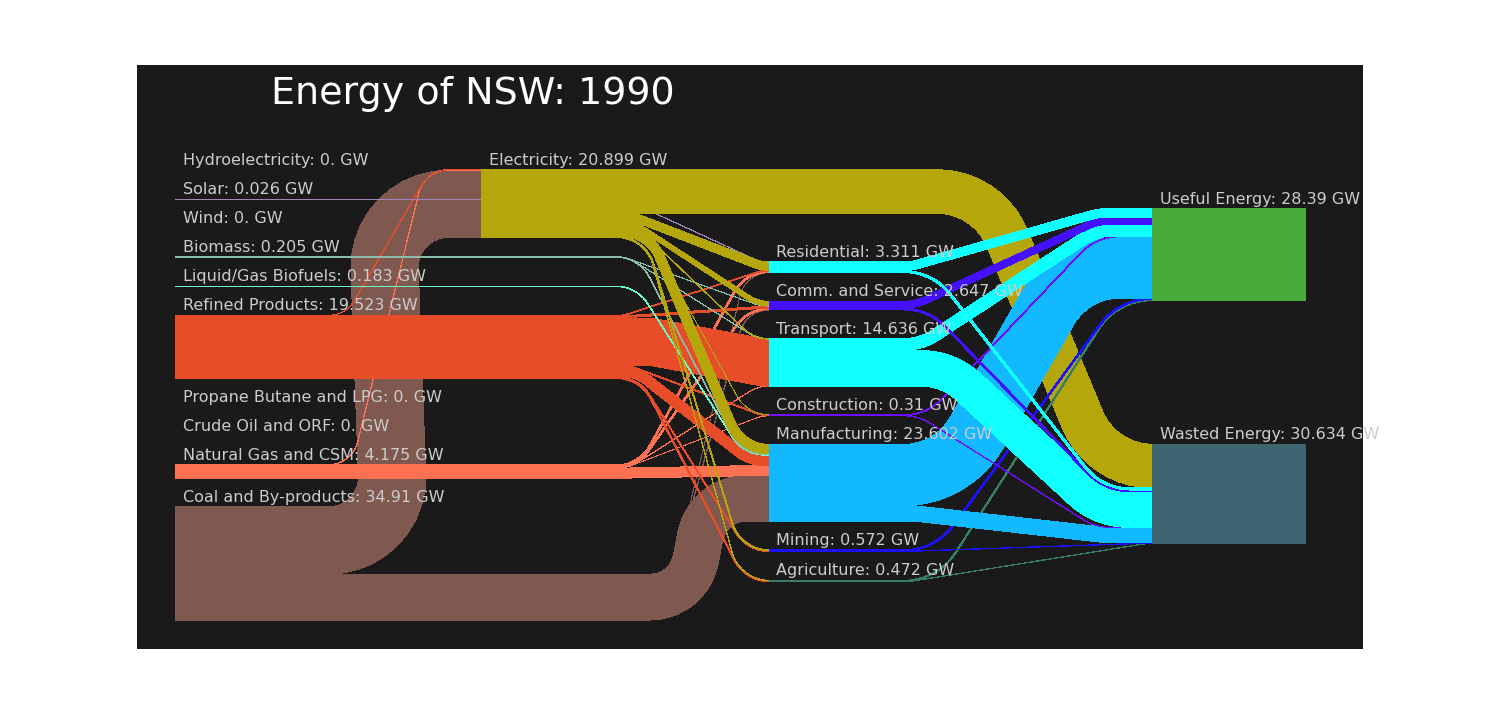

```mathematica
(*Here is the corresponding Sankey.*)maxBreadth=Module[{nodeNameList=nodeNames["AUS"],strandList=strands["NSW",1990]},Table[Max[sums[strandList,nodeNameList][[i,j]]],{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}]];
(*To normalize, we divide by the largest total energy flow in the time series.*)
normalizer=Module[{nodeNameList=nodeNames["AUS"],strandList=strands["NSW",1990]},(N[Max[Plus@@sums[strandList,nodeNameList][[1]]]])^-1];

betweenSpace=1.25 {0.12,.2,.12,0.6};(*set the space between nodes in each column*)
gaps={.8,.8,1.3}; (*set gaps between columns*)
widths={.8,.7,.7,.8}; (*set widths of nodes along direction of flow*)
startys={0,1.9,.2,-.2}; (*set the y offset of each column*)
drawSankey[strands["NSW",1990], nodeNames["AUS"], colors["AUS"], "Quads"(*this is stupid, just so we don't convert...*), "GW", True,1500,16,"Energy of "<>"NSW"<>": "<>ToString[1990],38,{.5,2.9},{{-.2,Plus@@gaps+Plus@@widths+.3},{0,3.05}}]
```

```mathematica
(*Here is a demonstration of the sub-sankey diagrams*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: "ifun" will be suppressed during this calculation.

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of NumberForm :: "sigz" will be suppressed during this calculation.

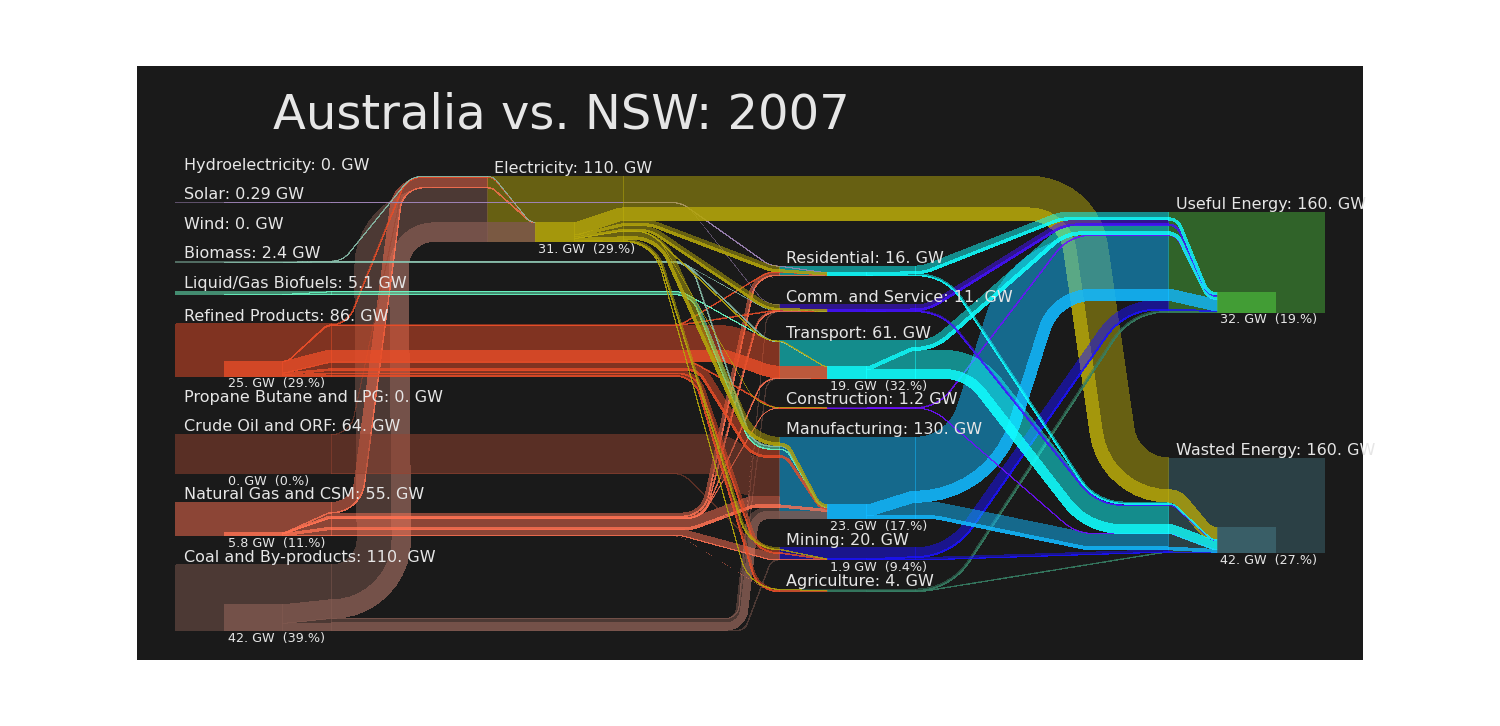

```mathematica
maxBreadth=Module[{nodeNameList=nodeNames["AUS"],strandList=strands["AUS",2007]},Table[Max[sums[strandList,nodeNameList][[i,j]]],{i,1,Length[nodeNameList]},{j,1,Length[nodeNameList[[i]] ]}]];
(*To normalize, we divide by the largest total energy flow in the time series.*)
normalizer=Module[{nodeNameList=nodeNames["AUS"],strandList=strands["AUS",2007]},(N[Max[Plus@@sums[strandList,nodeNameList][[1]]]])^-1];
(*We'll leave some space between nodes in the same column.  This space should be inversely proportional to the number of nodes in the column.*)
betweenSpace=1.25 {0.12,.2,.12,0.6};
gaps={.8,.8,1.3};
widths={.8,.7,.7,.8};
startys={0,1.9,.2,-.2};
subinset=.25;  (*set how far the subnodes are inset horizontally*)
drawSubSankey[strands["AUS",2007],strands["NSW",2007],nodeNames["AUS"], colors["AUS"],"Quads","Quads","GW", True,1500,16,"Australia vs. "<>"NSW"<>": "<>ToString[2007],38,{.5,2.8},{{-.2,Plus@@gaps+Plus@@widths+.2},{0,3.05}}]
```